```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/phy485-optics" ]

<<MaTeX`
```

\\wsl$\Ubuntu\home\pjoot\project\figures\phy485-optics

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

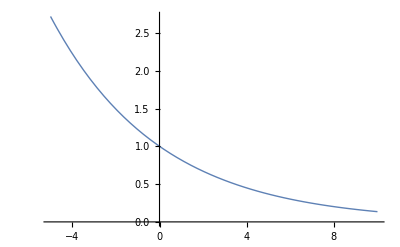

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
p = Plot[E^(-0.20 x), {x, -5, 10}, 
BaseStyle->texStyle,
AxesLabel -> { MaTeX["x"],MaTeX["e^{x/5}"]}, PlotStyle-> Thick]
```

```mathematica
peeters`exportForLatex["negativeExponentialPlotFig1", p]
```

{negativeExponentialPlotFig1.eps,negativeExponentialPlotFig1pn.png}